Метод Эйлера

|     x |     y
 |      2 |      4
 |  2.10000 |  4.40000
 |  2.20000 |  4.82020
 |  2.30000 |  5.26040
 |  2.40000 |  5.72070
 |  2.50000 |  6.20080
 |  2.60000 |  6.70080
 |  2.70000 |  7.22060
 |  2.80000 |  7.76020
 |  2.90000 |  8.31960
 |  3.00000 |  8.89880
 |  3.10000 |  9.49760
 |  3.20000 |  10.11600
 |  3.30000 |  10.75500
 |  3.40000 |  11.41300
 |  3.50000 |  12.09000
 |  3.60000 |  12.78800
 |  3.70000 |  13.50500
 |  3.80000 |  14.24100
 |  3.90000 |  14.99800
 |  4.00000 |  15.77400

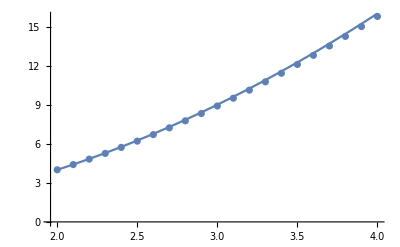

Метод Рунге-Кутты 4 степени

|     x |     y
 |      2 |      4
 |  2.10000 |  4.41000
 |  2.20000 |  4.84000
 |  2.30000 |  5.29000
 |  2.40000 |  5.76000
 |  2.50000 |  6.25000
 |  2.60000 |  6.76000
 |  2.70000 |  7.29000
 |  2.80000 |  7.84000
 |  2.90000 |  8.41000
 |  3.00000 |  9.00000
 |  3.10000 |  9.61000
 |  3.20000 |  10.24000
 |  3.30000 |  10.89000
 |  3.40000 |  11.56000
 |  3.50000 |  12.25000
 |  3.60000 |  12.96000
 |  3.70000 |  13.69000
 |  3.80000 |  14.44000
 |  3.90000 |  15.21000
 |  4.00000 |  16.00000

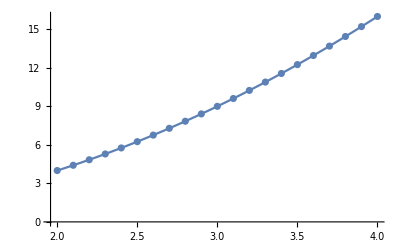

Встроенный метод NDSolve

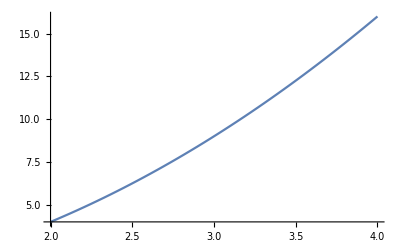

```mathematica
f[x_,y_]:=5+y (2 x-5)/x^2;
y0 = 4; a=2; b =4;h=0.1;
x0 = 2;
m = Floor[(b-a)/h]+1; 

x = x0; y=y0;
"Метод Эйлера"
(*Метод Эйлера*)
eul = Table[{x,y}={x+h,y+h*f[x,y]},{i,m-1}];
eul = Prepend[eul, {x0,y0}];

gr1:=ListPlot[eul]

g[x_]:=x*x;
gr2:=Plot[g[x],{x,a,b}]

lst={{}, {"    x","    y"}};
PaddedForm[TableForm[eul, TableHeadings->lst],{5,5}]
Show[{gr1,gr2}]

"Метод Рунге-Кутты 4 степени"
rk4[f_,x0_,y0_, h_, m_]:=Block[{k1,k2,k3,k4,x=x0, y=y0,t,k},
k1[x_,y_]:=h*f[x,y];
k2[x_,y_]:=h*f[x+h/2,y+k1[x,y]/2];
k3[x_,y_]:=h*f[x+h/2,y+k2[x,y]/2];
k4[x_,y_]:=h*f[x+h,y+k3[x,y]];
t=Table[{x,y} = {x+h,y+(k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6},{k,m-1}];
t=Prepend[t,{x0,y0}];
Return[t]]
tab1:=rk4[f,x0,y0,h,m]
gr3:=ListPlot[tab1]
lst={{}, {"    x","    y"}};
PaddedForm[TableForm[tab1, TableHeadings->lst],{5,5}]
Show[{gr3,gr2}]

"Встроенный метод NDSolve"

Clear[u,v];
solution = NDSolve[{v'[u]==f[u,v[u]],v[x0]==y0},v,{u,a,b}];
p[u_] := v[u]/.solution
gr4:=Plot[p[x],{x,a,b}]
Show[{gr4}]
```